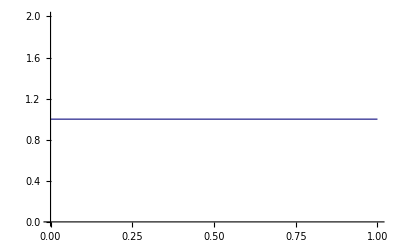

```mathematica
Plot[PDF[UniformDistribution[{0,1}],x],{x,0,1}]
```

```mathematica
a[p_] := PDF[BinomialDistribution[100,p],10]
```

```mathematica
a[0.1]
```

0.131865

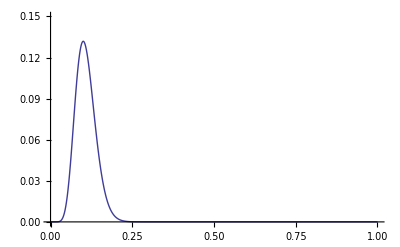

```mathematica
Plot[a[p],{p,0,1},PlotRange->{{0,1},{0,0.15}}]
```

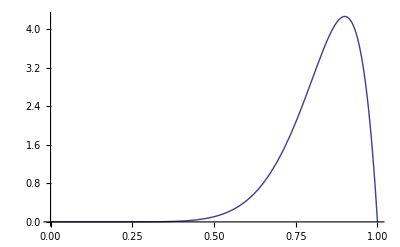

```mathematica
Plot[PDF[BetaDistribution[10,2],x],{x,0,1}]
```

```mathematica
b[p_] := a[p]*PDF[BetaDistribution[10,2],p]
```

```mathematica
b[0.05]
```

3.41174×10^-12

```mathematica
pdata = Integrate[b[p],{p,0,1}]
```

38038/2141356505661

```mathematica
posterior[p_] := b[p]/pdata
```

```mathematica
Integrate[posterior[p],{p,0,1}]
```

1

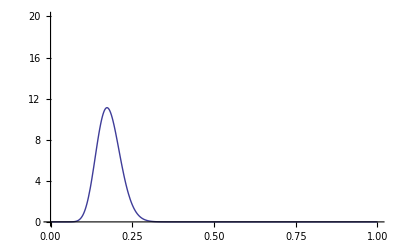

```mathematica
Plot[posterior[p],{p,0,1},PlotRange->{{0,1},{0,20}}]
```

```mathematica
Plot[PDF[BetaDistribution[10+10,100-10+2],x],{x,0,1},PlotRange->{{0,1},{0,20}}]
```

-Graphics-

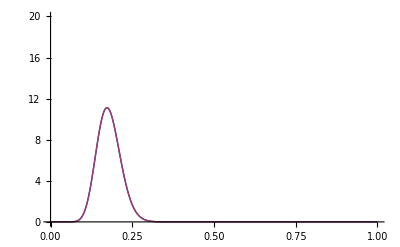

```mathematica
Plot[{posterior[p],PDF[BetaDistribution[10+10,100-10+2],p]},{p,0,1},PlotRange->{{0,1},{0,20}}]
```

## Now plotting the subplots for Book

```mathematica
plotprior1 := Plot[PDF[BetaDistribution[10,2],θ],{θ,0,1},PlotStyle->{Gray,Thickness[0.01]},BaseStyle->{FontSize->16},AxesLabel->{θ,pdf},PlotLabel->"Prior"]
```

```mathematica
likelihood1[p_,x_,n_] := PDF[BinomialDistribution[n,p],x]
```

```mathematica
plotlikelihood1[x_,n_] := Plot[likelihood1[p,x,n],{p,0,1},PlotRange->{{0,1},Full},PlotStyle->{Gray,Thickness[0.01]},BaseStyle->{FontSize->16},AxesLabel->{θ,likelihood},PlotLabel->"Likelihood"]
```

```mathematica
ppdata1[x_,n_] := Integrate[PDF[BetaDistribution[10,2],pp]*likelihood1[pp,x,n],{pp,0,1}]
```

```mathematica
posterior1[p_,x_,n_,pdatacalculated_] := PDF[BetaDistribution[10,2],p]*likelihood1[p,x,n]/pdatacalculated
```

```mathematica
plotposterior1[x_,n_,pdatacalculated_] := Plot[posterior1[p,x,n,pdatacalculated],{p,0,1},PlotRange->{{0,1},Full},PlotStyle->{Gray,Thickness[0.01]},BaseStyle->{FontSize->16},AxesLabel->{θ,pdf},PlotLabel->"Posterior"]
```

```mathematica
p1 = plotprior1;
```

```mathematica
p2 = plotlikelihood1[1,10];
pdatacalculated1 = ppdata1[1,10];
```

```mathematica
p3 = plotposterior1[1,10,pdatacalculated1];
```

```mathematica
p4 = plotprior1;
```

```mathematica
p5 = plotlikelihood1[10,100];
pdatacalculated2 = ppdata1[10,100];
p6 = plotposterior1[10,100,pdatacalculated2];
p7 = plotprior1;
p8 = plotlikelihood1[100,1000];
pdatacalculated3 = ppdata1[100,1000];
p9 =plotposterior1[100,1000,pdatacalculated3];
```

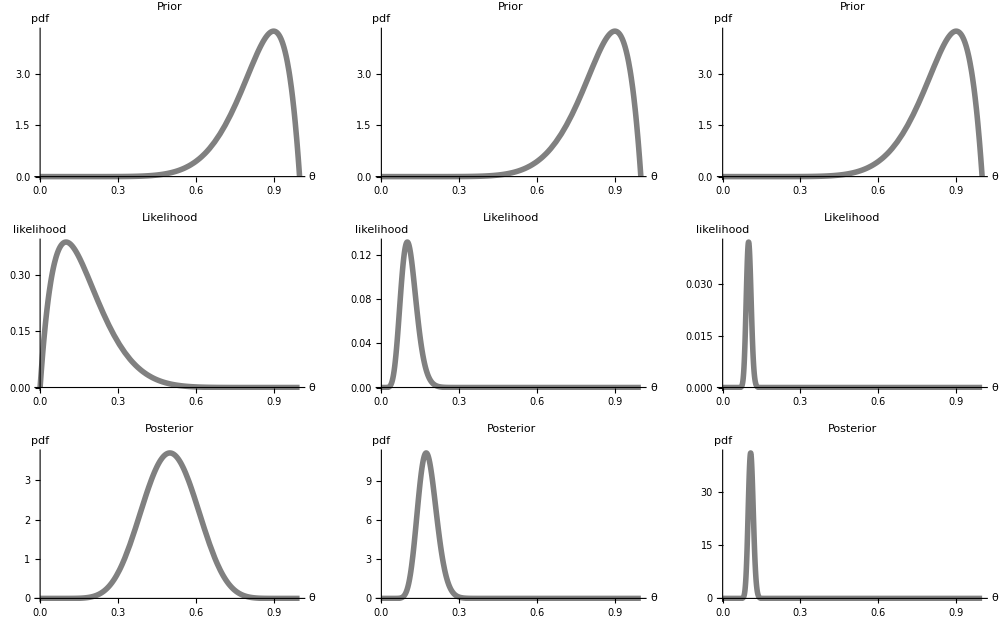

```mathematica
Show[GraphicsGrid[{{p1,p4,p7},{p2,p5,p8},{p3,p6,p9}}],ImageSize->1000]
```